## Stationary phase point estimation

Setup the triangulation and load the data

```mathematica
config="curvyconfig2";
λ= 20;
xth=λ 1.26413;
spinstr=ToString[2λ];
SetDirectory[NotebookDirectory[]];
nomefile=StringJoin["d3-dist4-bf_",Flatten@Table[{spinstr,"."},17],spinstr,"_","0.",ToString[6 λ],"_0.",config,".dat"];
data= Import["data_final/"<>nomefile, "Table"];
```

Fiducial interval length and normalization

```mathematica
c=Round[Sqrt[Length[data]]/2.-1];
norm=Total[data[[All,2]] + ⅈ data[[All,3]],Method->"CompensatedSummation"]//Abs;
```

Definition of partial and running sums

```mathematica
s[x_] := Total[Part[(data[[All,2]] + ⅈ data[[All,3]])/norm, 1;;x]]
ref= s[Length[data]];
psum = Table[{data[[1]][[1]]/2+x-1,s[x]/ref}, {x,1,Length[data],1}];
rs[x_,c_] := Total[Part[(data[[All,2]] + ⅈ data[[All,3]])/norm, x-c;;x+c]]
rsum[c_] = Table[{data[[1]][[1]]/2+x-1,rs[x,c]/ref}, {x,1+c,Length[data]-c,1}];
rav[c_] := Table[{rsum[c][[x,1]],Total[Part[rsum[c][[All,2]]/(2c), x-c;;x+c]]//Abs}, {x,1+c,Length[rsum[c]]-c,1}];
```

Calculation of all the interval sizes we correlate

```mathematica
lowc =Round[0.5Sqrt[Length[data]]/2.-1];
highc =Round[1.5Sqrt[Length[data]]/2.-1]+1;
windows=Subsets[Range[lowc,highc],{3}];
```

We repeat the algorithm multiple times to obtain a result that is as independent as possible from the window size.

```mathematica
Trim[lista_,min_,max_]:=Select[lista,min<=First[#]<=max&]
```

```mathematica
i=1;
Do[
{c1,c2,c3}=test;
runningAverageW1=rav[c1];
runningAverageW2=rav[c2];
runningAverageW3=rav[c3];
len=Min[runningAverageW1//Length,runningAverageW2//Length,runningAverageW3//Length];
listacorta =First@ Select[{runningAverageW1,runningAverageW2,runningAverageW3},Length[#]==len&];
{min,max} = First/@{First[listacorta],Last[listacorta]};
filteraverage=Table[{First@Trim[runningAverageW3,min,max][[idx]],Last[Trim[runningAverageW1,min,max][[idx]]]Last[Trim[runningAverageW2,min,max][[idx]]]Last[Trim[runningAverageW3,min,max][[idx]]]},{idx,1,len}];
norm2=Max[filteraverage[[All,2]]];
Do[filteraverage[[i,2]]=filteraverage[[i,2]]/norm2,{i,1,filteraverage//Length}];
Do[If[filteraverage[[i,2]]<10^-3,filteraverage[[i,2]]=0],{i,1,filteraverage//Length}];
peaks[i++]=filteraverage[[First/@FindPeaks[Last/@filteraverage,10]]];
,{test,windows}]
```

Positions of all the peaks, average an standard deviation. Rounded to integers

```mathematica
peaksdata=First/@Flatten[peaks/@Range[Length[windows]],1];
```

```mathematica
mean=Round[N[Mean@peaksdata]];
```

```mathematica
stdev=Ceiling[StandardDeviation@peaksdata];
```

## Plots

Preparing the red line (geometric area) and the green band (numerical estimate)

```mathematica
Theory= {RGBColor[0.63,0,0],Thickness[.002],Line[{{xth ,-3},{xth ,3}}]};
Numerics = {LightGreen,Rectangle[{Floor[mean-stdev],3},{Ceiling[mean+stdev],-3}], Darker@ Darker@Green,Dashed,Line[{{Floor[mean-stdev],3},{Floor[mean-stdev],-3}}], Darker@ Darker@Green,Dashed,Line[{{Ceiling[mean+stdev],3},{Ceiling[mean+stdev],-3}}]};
```

We use MaTeX for format the labels

```mathematica
<<MaTeX`
```

```mathematica
fsize=45;
```

```mathematica
xtics= {#,MaTeX[#,FontSize->fsize]}&/@{20,40,60,80};
ytics= {ToExpression[#],MaTeX[#,FontSize->fsize]}&/@{"3.0","2.0","1.0","-1"};
xlabel= MaTeX["x",FontSize->fsize];
ylabel= MaTeX["\\text{Re}P_w(x)",FontSize->fsize];
```

Partial Sum

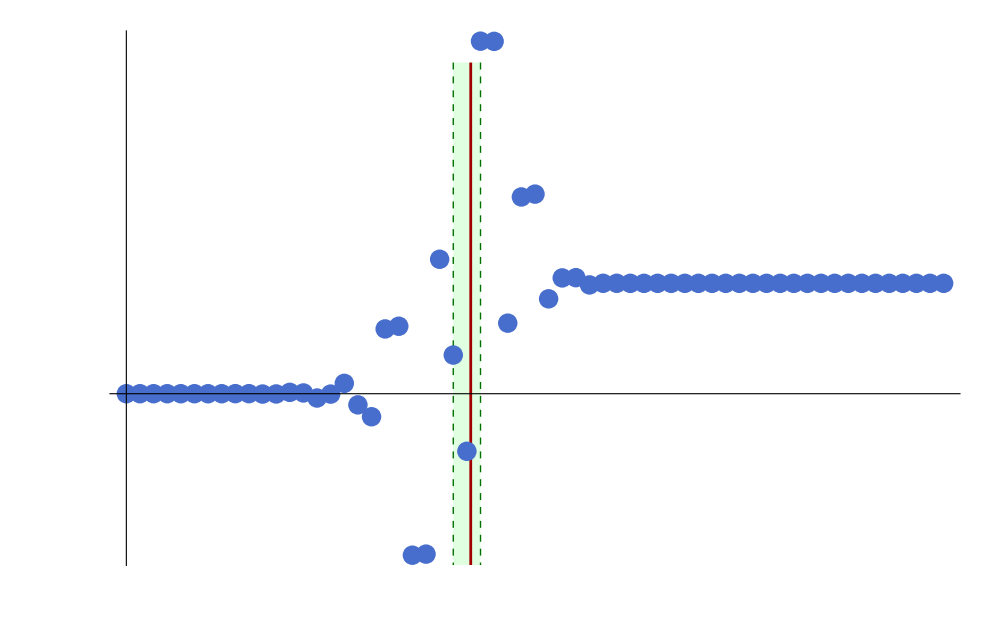

```mathematica
plot1=ListPlot[Re[psum],PlotStyle->RGBColor[0.28,0.43,0.8],PlotMarkers->{Automatic,20},ImageSize->1000,PlotRange->All,AxesLabel->{xlabel,ylabel},Ticks->{xtics,ytics},Prolog->{Numerics,Theory}]
```

```mathematica
runningAverageW1=rav[1];
runningAverageW2=rav[3];
runningAverageW3=rav[5];
len=Min[runningAverageW1//Length,runningAverageW2//Length,runningAverageW3//Length];
shortlist =First@ Select[{runningAverageW1,runningAverageW2,runningAverageW3},Length[#]==len&];
{min,max} = First/@{First[shortlist],Last[shortlist]};
filteraverage=Table[{First@Trim[runningAverageW3,min,max][[idx]],Last[Trim[runningAverageW1,min,max][[idx]]]Last[Trim[runningAverageW2,min,max][[idx]]]Last[Trim[runningAverageW3,min,max][[idx]]]},{idx,1,len}];
filteraverage ={filteraverage[[#,1]],filteraverage[[#,2]]/Max[filteraverage[[All,2]]]}&/@Range[1,filteraverage//Length];
```

```mathematica
ylabelr= MaTeX["\\overline{ R_w}(x)",FontSize->fsize];
ytics= {ToExpression[#],MaTeX[#,FontSize->fsize]}&/@{"1.0","0.6","0.2"};
```

Averaged running Sum

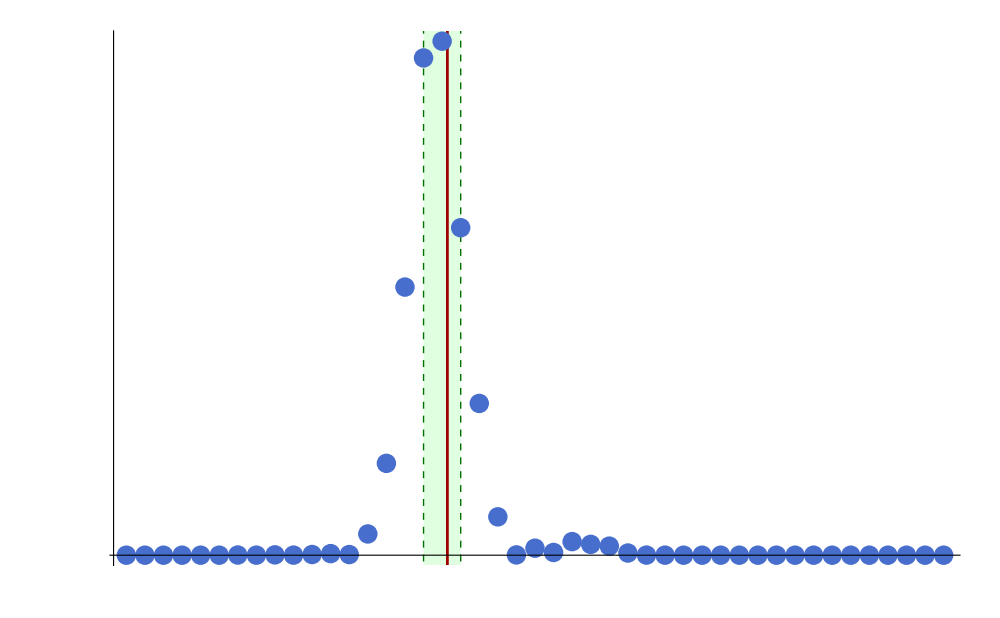

```mathematica
plot2=ListPlot[Re[filteraverage],PlotStyle->RGBColor[0.28,0.43,0.8],PlotMarkers->{Automatic,20},ImageSize->1000,PlotRange->All,AxesLabel->{xlabel,ylabelr},Ticks->{xtics,ytics},Prolog->{Numerics,Theory}]
```